# Solución del taller. Proyecto Final AAC.

## Presentado a: Jose Luis Ramirez R. Presentado por: Douglas Velasquez, Beimar Naranjo, Carlos Nosa.

## Problema 1

```mathematica
FactorInteger[2022]
```

{{2,1},{3,1},{337,1}}

```mathematica
F[Pe_,D_,Qu_]:=Module[{k,A,P,Q,A1,A2,B,B1,B2,G,G1,G2,a,R},R={};a=Floor[Sqrt[2022]];P=Pe;Q=Qu;k=0;
B1=0;
A1=1;A2=0;B2=1;G2=-P;G1=Q;A=0;B=0;
While[k<6, a=Floor[(P+Sqrt[2022])/Q];If[k==0,A=a;B=1;G=a];
If[k≠0,A=a A1+A2;A2=A1;A1=A;B=a B1+B2;B2=B1;B1=B;G=a G1+G2;
G2=G1;G1=G;P=a Q-P;
Q=(D-P^2)/Q;AppendTo[R,a]];k++];Return[R]]
```

```mathematica
F[0,2022,1]
```

{44,1,28,1,88}

```mathematica
ContinuedFraction[Sqrt[2022]]
```

{44,{1,28,1,88}}

## Problema 3.

```mathematica
Farey[n_]:=Join[{0},Union[Table[i/j,{j,n},{i,j-1}]//Flatten],{1}]
Mediant[a_,b_]:=(Numerator[a]+Numerator[b])/(Denominator[a]+Denominator[b])

ArbolFarey[n_]:= Module[{V,Ed},V=Farey[n];Ed={};
For[i=1,i≤Length[V],i++,
	For[j=i+1,j≤Length[V],j++,
		If[Abs[Numerator[V[[i]]]*Denominator[V[[j]]]- Numerator[V[[j]]]*Denominator[V[[i]]] ]==1,
			AppendTo[Ed,V[[i]]<->V[[j]] ]]]];
Graph[V,Ed,VertexLabels->"Name",VertexCoordinates->Table[{10*V[[i]],(1-Denominator[V[[i]]])},{i,1,Length[V]}],VertexStyle->Black,EdgeStyle->Red,VertexSize->Medium,ImageSize->Large]]
```

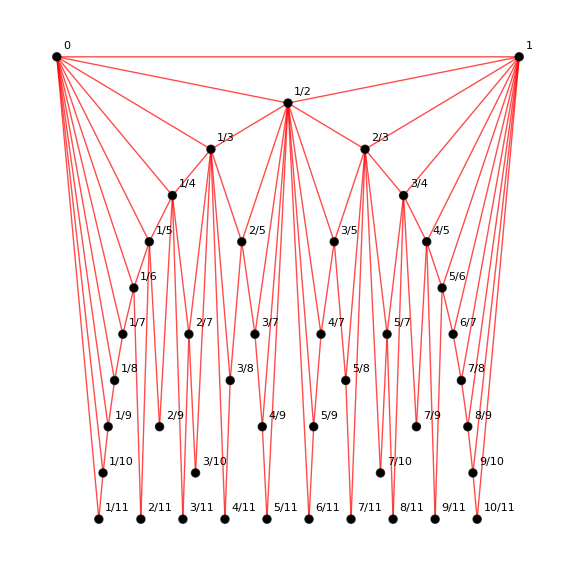

```mathematica
ArbolFarey[11]
```

## Problema 4.“Descenso por el árbol de Stern-Brocot”

```mathematica
SternBrocot[x_,n_]:=Module[{a={0,1},b={1,0},c={1,1},c0={0,1},l={0},convergent={},d=1,k=1},
While[Length[l]<n+1,
c[[1]]=a[[1]]+b[[1]];
c[[2]]=a[[2]]+b[[2]];
If[x==c[[1]]/c[[2]],
AppendTo[convergent,c[[1]]/c[[2]]];
l[[k]]++;
k++;
Break[],
If[x>c[[1]]/c[[2]],
If[d==1,l[[k]]++,
AppendTo[l,1];
d=1;
k++;
AppendTo[convergent,c0[[1]]/c0[[2]]]];
a[[1]]=c[[1]];
a[[2]]=c[[2]],
If[d==-1, l[[k]]++,
AppendTo[l,1];
d=-1;
k++;
AppendTo[convergent,c0[[1]]/c0[[2]]]];
b[[1]]=c[[1]];
b[[2]]=c[[2]]]];
c0[[1]]=c[[1]];
c0[[2]]=c[[2]]];
Print["Listado de convergentes:",convergent];
Print["Fracción de la última convergente:",Take[l,k-1]]]
```

```mathematica
SternBrocot[322/415,7]
```

Listado de convergentes:{0,1,3/4,7/9,45/58,322/415}

Fracción de la última convergente:{0,1,3,2,6,7}

```mathematica
Convergents[322/415]
```

{0,1,3/4,7/9,45/58,322/415}

```mathematica
ContinuedFraction[322/415]
```

{0,1,3,2,6,7}

## Problema 5

### b)

```mathematica
Farey[n_]:=Join[{0},Union[Table[i/j,{j,n},{i,j-1}]//Flatten],{1}]

SquareFarey[n_]:=Module[{F,G},F=Farey[n];G={Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]}; 
For[i=1,i≤Length[F],i++,For[j=1,j≤Length[F],j++,If[Abs[Numerator[F[[i]]]*Denominator[F[[j]]]-Numerator[F[[j]]]*Denominator[F[[i]]]]==1,
AppendTo[G,Line[{{F[[i]],0},{F[[i]],1/Denominator[F[[i]] ]}}]]; 
If[MemberQ[F,Mediant[F[[i]],F[[j]]]],AppendTo[G,Line[{{F[[i]],0}, {F[[j]],1/Denominator[F[[j]] ]}} ]];AppendTo[G,Line[{{F[[i]],1/Denominator[F[[i]] ]}, {F[[j]],0}} ]]];]]] ; 
For[i=1,i≤Length[F],i++,AppendTo[G,Text[Style[F[[i]],Black,FontSize->8],{F[[i]],-1/8}]]];
DeleteDuplicates[G]]
```

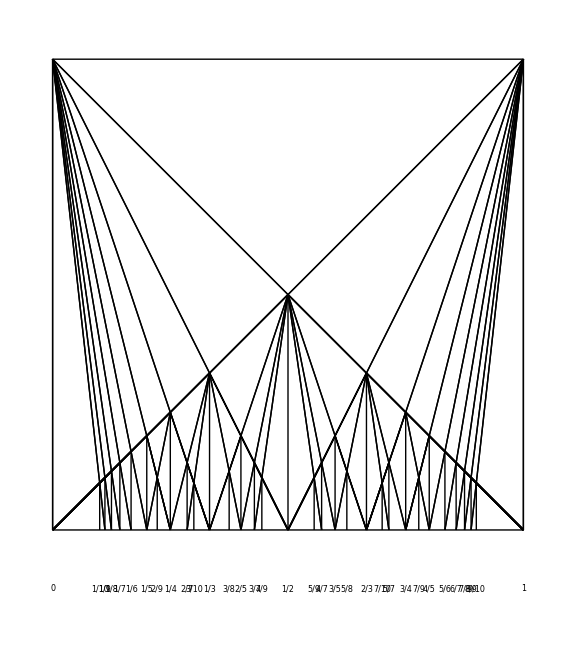

```mathematica
Graphics[SquareFarey[10],ImageSize->Large]
```

## Problema 8

### a)

24/67

```mathematica
ContinuedFraction[24/67]
```

{0,2,1,3,1,4}

e con 5 grados de aproximación

```mathematica
ContinuedFraction[E,5]
```

{2,1,2,1,1}

719/1001

```mathematica
ContinuedFraction[719/1001]
```

{0,1,2,1,1,4,1,1,6,2}

### b)

```mathematica
Farey[n_]:=Join[{0},Union[Table[i/j,{j,n},{i,j-1}]//Flatten],{1}]
Mediant[a_,b_]:=(Numerator[a]+Numerator[b])/(Denominator[a]+Denominator[b])

FractionFarey[x_,n_]:=Module[{CF,a,b,piv,FF}, 
If[Element[x,Rationals],CF=ContinuedFraction[x],CF=ContinuedFraction[x,n]]; 
b=1; a=First[CF]; FF={a};
For[i=2,i≤Length[CF],i++,piv=a; a=b; b=piv; For[j=1,j≤CF[[i]],j++,If[i==2 &&j==1,a=a+b,a=Mediant[a,b]]]; AppendTo[FF,a]]; 
FF]
```

24/67

```mathematica
FractionFarey[24/67,0]
```

{0,1/2,1/3,4/11,5/14,24/67}

```mathematica
Convergents[24/67,6]
```

{0,1/2,1/3,4/11,5/14,24/67}

e con 5 grados de aproximación

```mathematica
FractionFarey[E,5]
```

{2,3,8/3,11/4,19/7}

```mathematica
Convergents[E,5]
```

{2,3,8/3,11/4,19/7}

719/1001

```mathematica
FractionFarey[719/1001,0]
```

{0,1,2/3,3/4,5/7,23/32,28/39,51/71,334/465,719/1001}

```mathematica
Convergents[719/1001,10]
```

{0,1,2/3,3/4,5/7,23/32,28/39,51/71,334/465,719/1001}

## Problema 9

```mathematica
TriangleFarey[x_,n_]:=Module[{CF,FF,P,G,a,b,piv,K,Tt},G={};Tt={}; If[Element[x,Rationals],CF=ContinuedFraction[x],CF=ContinuedFraction[x,n]];b=1; a=First[CF]; FF={a};K={a};For[i=2,i≤Length[CF],i++,piv=a; a=b; b=piv; For[j=1,j≤CF[[i]],j++,If[i==2 &&j==1,a=a+b,a=Mediant[a,b]; AppendTo[K,a]]]; AppendTo[FF,a]]; K=Select[K,MemberQ[FF,#]==False &]; P=Table[{k,Mod[k,2]},{k,-1,Length[FF]-1}]; If[P[[-1,2]]==0,AppendTo[G,Line[{{0,0},P[[-1]]}]];AppendTo[G,Line[{P[[1]],P[[-2]]}]],AppendTo[G,Line[{{0,0},P[[-2]]}]];AppendTo[G,Line[{P[[1]],P[[-1]]}]]]; AppendTo[G,{Thick,Line[P]}]; For[i=2,i≤Length[FF]+1,i++,AppendTo[G,Text[Style[FF[[i-1]],Black,FontSize->12],{i-2,Mod[i-2,2]-(0.25)*(-1)^(Mod[i-2,2])} ]]]; AppendTo[G,Text[Style["1/0",Black,FontSize->12],{-1,1+0.25}]]; For[i=2,i≤Length[CF],i++,For[j=1,j≤CF[[i]]-1,j++,AppendTo[G,Line[{P[[i]],{P[[i-1,1]]+2*j/(CF[[i]]),Mod[P[[i,2]]+1,2]}}]]; AppendTo[Tt,{P[[i-1,1]]+2*j/(CF[[i]]),Mod[P[[i,2]]+1,2]+(0.25)*(-1)^(Mod[i,2])}] ]]; For[k=1,k≤Length[K],k++,AppendTo[G,Text[Style[K[[k]],Black,FontSize->12],Tt[[k-1+CF[[2]]]]]]];
For[k=1,k≤CF[[2]]-1,k++,AppendTo[G,Text[Style[1/k,Black,FontSize->12],Tt[[k]]]]];
For[h=2,h≤ Length[CF],h++,AppendTo[G,Text[Style[CF[[h]],Thick,Orange,FontSize->20],{h-2,1/2}]]];
 G ]
```

24/67

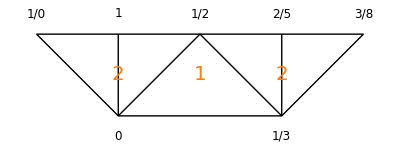

```mathematica
Graphics[TriangleFarey[3/8,0],ImageSize->Full]
```

e con 5 grados de aproximación

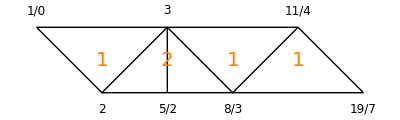

```mathematica
Graphics[TriangleFarey[E,5],ImageSize->Full]
```

719/1001

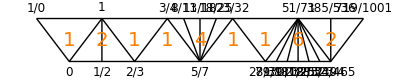

```mathematica
Graphics[TriangleFarey[719/1001,0],ImageSize->Full]
```

## Problema 10

```mathematica
Farey[n_]:=Join[{0},Union[Table[i/j,{j,n},{i,j-1}]//Flatten],{1}]
Mediant[a_,b_]:=(Numerator[a]+Numerator[b])/(Denominator[a]+Denominator[b])
```

```mathematica
FareyCircle[n_,k_]:=Module[{T,F,kinf,ksup},T={}; F=Farey[n];kinf=k[[1]];ksup=k[[2]];
For[i=1,i≤Length[F],i++,
	For[j=1,j≤Length[F],j++, If[Abs[Numerator[F[[i]]]*Denominator[F[[j]]]- Numerator[F[[j]]]*Denominator[F[[i]]]]==1, 
		For[h=kinf,h≤ksup,h++, AppendTo[T,{Dashing[Tiny],Circle[{(F[[i]]+F[[j]])/2+h,0},Abs[F[[i]]-F[[j]]]/2,{0,Pi}]}] ] ] ]]; 
T=DeleteDuplicates[T]; 

AppendTo[T,Text[Style["1/0",Black,FontSize->8],{ksup+1-1/2^6,3/4}]];
AppendTo[T,Text[Style[ksup+1,Black,FontSize->12],{ksup+1,-1/8}]];
For[h=kinf,h≤ksup,h++,
AppendTo[T,{Dashing[Tiny],Line[{{h,3/4},{h,0},{h+1,0},{h+1,3/4}}]}];
AppendTo[T,Text[Style["1/0",Black,FontSize->8],{h+-1/2^6,3/4}]];  
AppendTo[T,Text[Style[h,Black,FontSize->12],{h,-1/8}]]; 
];
T]

FractionFarey[x_,n_]:=Module[{CF,a,b,piv,FF}, 
If[Element[x,Rationals],CF=ContinuedFraction[x],CF=ContinuedFraction[x,n]]; 
b=1; a=First[CF]; FF={a};
For[i=2,i≤Length[CF],i++,piv=a; a=b; b=piv; For[j=1,j≤CF[[i]],j++,If[i==2 &&j==1,a=a+b,a=Mediant[a,b]]]; AppendTo[FF,a]]; 
FF]
```

```mathematica
SemiCircle[t_,a_,b_]:= Module[{T},If[b>a,T={Thick,Red,Circle[{(a+b)/2,0},Abs[b-a]/2,{Pi,Pi-Pi*t}]},T={Thick,Red,Circle[{(a+b)/2,0},Abs[b-a]/2,{0,Pi*t}]}]; T]

SemiCirclesList[t_,L_]:=Module[{T,Tl},If[-1≤t≤1 ,
If[-1≤t≤0,T={Thick,Red,Line[{{First[L],3/4},{First[L],-3*t/4}}]},T={{Thick,Red,Line[{{First[L],3/4},{First[L],0}}]},SemiCircle[t,L[[1]],L[[2]]]}],
	T=Table[SemiCircle[1,L[[i]],L[[i+1]]],{i,1,Floor[t]}]; PrependTo[T,{Thick,Red,Line[{{First[L],3/4},{First[L],0}}]}] ; AppendTo[T,SemiCircle[t-Floor[t],L[[Floor[t]+1]],L[[Floor[t]+2]] ] ] ]; 
For[i=1,i≤Length[L],i++,AppendTo[T,Text[Style[Numerator[L[[i]]]/Denominator[L[[i]]],Red,FontSize->16],{L[[i]],-1/2^4}]]]; 
T=Union[T,FareyCircle[25,{First[L],First[L]}]]; 
Graphics[T,ImageSize->Large]]
```

```mathematica
Pinball[x_,n_]:= Manipulate[SemiCirclesList[t,FractionFarey[x,n]],{t,-1,Length[FractionFarey[x,n]]-1-0.001},ControlType->Animator,ControlPlacement->Bottom]
```

```mathematica
Pinball[E,6]
```